```mathematica
In this code  α and  β are the orders of the ellitic generators so
```

and are code ellitic generators In of orders so the^2 this α β

Generators of order 5, 5

```mathematica
α=ⅇ^(ⅈ π/5);
β=ⅇ^(ⅈ π/5);
```

```mathematica
The recursion formula depends on whether the numerator of the Farey fraction is odd or even
```

depends even Farey formula fraction is numerator odd of on or recursion the^2 The whether

```mathematica
LeftFraction[p_,q_]:=
(frac=FareySequence[q,Position[FareySequence[q],p/q][[1]][[1]]-1];
{Numerator[frac],Denominator[frac]});
```

```mathematica
RightFraction[p_,q_]:=
(frac=FareySequence[q,Position[FareySequence[q],p/q][[1]][[1]]+1];
{Numerator[frac],Denominator[frac]});
```

```mathematica
ClearAll[FareyPolynomial]
```

```mathematica
FareyPolynomial[0,1,α_,β_]:=α/β+β/α-z;
FareyPolynomial[1,1,α_,β_]:=α β+1/(α β)+z;
FareyPolynomial[1,2,α_,β_]:=2+(α β-α/β-β/α+1/(α β))z+z^2;
```

```mathematica
FareyPolynomial[p_,q_,α_,β_]:=Module[{p1,p2,q1,q2},
{p1,q1}=LeftFraction[p,q];
{p2,q2}=RightFraction[p,q];
Expand[4+1/α^2+α^2+1/β^2+β^2-FareyPolynomial[p1,q1,α,β]*FareyPolynomial[p2,q2,α,β]-FareyPolynomial[Abs[p2-p1],Abs[q2-q1],α,β]]]/;EvenQ[q];
```

```mathematica
FareyPolynomial[p_,q_,α_,β_]:=Module[{p1,p2,q1,q2},
{p1,q1}=LeftFraction[p,q];
{p2,q2}=RightFraction[p,q];
Expand[2(α β+α/β+β/α+1/(α β))-FareyPolynomial[p1,q1,α,β]*FareyPolynomial[p2,q2,α,β]-FareyPolynomial[Abs[p2-p1],Abs[q2-q1],α,β]]]/;OddQ[q];
```

```mathematica
FareyPolynomial[1,3,α,β]
```

ⅇ^(-(2 ⅈ π)/5)+ⅇ^((2 ⅈ π)/5)+5 z-2 ⅇ^(-(2 ⅈ π)/5) z-2 ⅇ^((2 ⅈ π)/5) z-4 z^2+ⅇ^(-(2 ⅈ π)/5) z^2+ⅇ^((2 ⅈ π)/5) z^2+z^3

```mathematica
B={FareyPolynomial[1,2,α,β],
FareyPolynomial[1,3,α,β],
FareyPolynomial[1,4,α,β],
FareyPolynomial[3,4,α,β],
FareyPolynomial[1,5,α,β],
FareyPolynomial[2,5,α,β],
FareyPolynomial[3,5,α,β],
FareyPolynomial[4,5,α,β],
FareyPolynomial[1,6,α,β],
FareyPolynomial[5,6,α,β],
FareyPolynomial[1,7,α,β],
FareyPolynomial[2,7,α,β],
FareyPolynomial[3,7,α,β],
FareyPolynomial[4,7,α,β],
FareyPolynomial[5,7,α,β],
FareyPolynomial[6,7,α,β],
FareyPolynomial[1,8,α,β],
FareyPolynomial[3,8,α,β],
FareyPolynomial[5,8,α,β],
FareyPolynomial[7,8,α,β],
FareyPolynomial[1,9,α,β],
FareyPolynomial[2,9,α,β],
FareyPolynomial[4,9,α,β],
FareyPolynomial[5,9,α,β],
FareyPolynomial[7,9,α,β],
FareyPolynomial[8,9,α,β]}
```

```mathematica
Length[B]
```

26

```mathematica
Result={};
For[i=1, i<Length[B]+1, i++,
{ℽ=NRoots[B[[i]]==-2,z];
{Result=AppendTo[Result,N[ℽ]],Print[N[ℽ],i]}}];
```

```mathematica
Length[Result]
```

26

```mathematica
List1={0.6909830056250525-1.8768437563999216 ⅈ,0.6909830056250525+1.8768437563999216 ⅈ,
1.9258572011577797-1.3654093549482897 ⅈ,
1.9258572011577797+1.3654093549482897 ⅈ,
0.1908417229991798-0.7285489456644908 ⅈ,
0.1908417229991798+0.7285489456644908 ⅈ,
2.5001412826258727-0.8952253358642928 ⅈ,
2.5001412826258727+0.8952253358642928 ⅈ,
-1.1181752713757676-0.8952253358642928 ⅈ,-1.1181752713757676+0.8952253358642928 ⅈ,
1.1911242882509254-0.7285489456644908 ⅈ,
1.1911242882509254+0.7285489456644908 ⅈ,
0.9187282929232751-0.890981701394998 ⅈ,
0.9187282929232751+0.890981701394998 ⅈ,
2.865848795323506-0.5708828935364273 ⅈ,
2.865848795323506+0.5708828935364273 ⅈ,
0.0582184568732739-0.70911919591475 ⅈ,
0.0582184568732739+0.70911919591475 ⅈ,
1.378008915469814-1.509457192441404 ⅈ,
1.378008915469814+1.509457192441404 ⅈ,
0.003957095780291017-1.509457192441404 ⅈ,0.003957095780291017+1.509457192441404 ⅈ,
1.3237475543768313-0.70911919591475 ⅈ,
1.3237475543768313+0.70911919591475 ⅈ,
-1.483882784073401-0.5708828935364273 ⅈ,
-1.483882784073401+0.5708828935364273 ⅈ,
0.4632377183268301-0.890981701394998 ⅈ,
0.4632377183268301+0.890981701394998 ⅈ,
0.10302665520922337-0.36272754627851456 ⅈ,0.10302665520922337+0.36272754627851456 ⅈ,
1.459773918892159-0.839349852326777 ⅈ,
1.459773918892159+0.839349852326777 ⅈ,
3.1281824315236704-0.3688973235186673 ⅈ,
3.1281824315236704+0.3688973235186673 ⅈ,
-1.746216420273565-0.3688973235186673 ⅈ,
-1.746216420273565+0.3688973235186673 ⅈ,
-0.0778079076420539-0.839349852326777 ⅈ,
-0.0778079076420539+0.839349852326777 ⅈ,
1.2789393560408817-0.36272754627851456 ⅈ,1.2789393560408817+0.36272754627851456 ⅈ,
0.5574456608899351-0.5390751755280065 ⅈ,
0.5574456608899351+0.5390751755280065 ⅈ,
1.864707092778132-0.7053005151797214 ⅈ,
1.864707092778132+0.7053005151797214 ⅈ,
3.318295812177286-0.24676526782070374 ⅈ,
3.318295812177286+0.24676526782070374 ⅈ,-0.11656011759558056-0.36748372266860313 ⅈ,-0.11656011759558056+0.36748372266860313 ⅈ,1.1602851447799893-0.8010424174516582 ⅈ,
1.1602851447799893+0.8010424174516582 ⅈ,
2.197588980185833-1.0511307695628667 ⅈ,

2.197588980185833+1.0511307695628667 ⅈ,
0.4286360136990782-1.130456016061194 ⅈ,
0.4286360136990782+1.130456016061194 ⅈ,
1.1207941697619255-1.5697356503004116 ⅈ,
1.1207941697619255+1.5697356503004116 ⅈ,
1.6039854969181389-0.6472107423073447 ⅈ,
1.6039854969181389+0.6472107423073447 ⅈ,
-0.2220194856680337-0.6472107423073447 ⅈ,-0.2220194856680337+0.6472107423073447 ⅈ,
0.2611718414881798-1.5697356503004116 ⅈ,
0.2611718414881798+1.5697356503004116 ⅈ,
0.953329997551027-1.130456016061194 ⅈ,
0.953329997551027+1.130456016061194 ⅈ,
-0.8156229689357279-1.0511307695628667 ⅈ,-0.8156229689357279+1.0511307695628667 ⅈ,0.22168086647011573-0.8010424174516582 ⅈ,0.22168086647011573+0.8010424174516582 ⅈ,1.4985261288456857-0.36748372266860313 ⅈ,1.4985261288456857+0.36748372266860313 ⅈ,-1.9363298009271805-0.24676526782070374 ⅈ,-1.9363298009271805+0.24676526782070374 ⅈ,-0.4827410815280268-0.7053005151797214 ⅈ,-0.4827410815280268+0.7053005151797214 ⅈ,
0.82452035036017-0.5390751755280065 ⅈ,
0.82452035036017+0.5390751755280065 ⅈ,
0.06435384103976118-0.21191919251258168 ⅈ,0.06435384103976118+0.21191919251258168 ⅈ,0.9784434039940513-0.6119469917163619 ⅈ,
0.9784434039940513+0.6119469917163619 ⅈ,
2.191503091760727-0.5559984486928047 ⅈ,
2.191503091760727+0.5559984486928047 ⅈ,
3.456682668830513-0.17145150324842157 ⅈ,
3.456682668830513+0.17145150324842157 ⅈ,
-0.1444810043037536-0.3493665020668438 ⅈ,-0.1444810043037536+0.3493665020668438 ⅈ,
0.8577590092702747-0.9902478914653399 ⅈ,
0.8577590092702747+0.9902478914653399 ⅈ,
1.5808927300720323-1.400065039455372 ⅈ,
1.5808927300720323+1.400065039455372 ⅈ,
1.7787782818366042-0.7016582074758307 ⅈ,
1.7787782818366042+0.7016582074758307 ⅈ,
-0.3968122705864991-0.7016582074758307 ⅈ,-0.3968122705864991+0.7016582074758307 ⅈ,-0.19892671882192722-1.400065039455372 ⅈ,-0.19892671882192722+1.400065039455372 ⅈ,
0.5242070019798305-0.9902478914653399 ⅈ,
0.5242070019798305+0.9902478914653399 ⅈ,
1.5264470155538588-0.3493665020668438 ⅈ,
1.5264470155538588+0.3493665020668438 ⅈ,
-2.074716657580408-0.17145150324842157 ⅈ,-2.074716657580408+0.17145150324842157 ⅈ,-0.8095370805106217-0.5559984486928047 ⅈ,-0.8095370805106217+0.5559984486928047 ⅈ,
0.4035226072560538-0.6119469917163619 ⅈ,
0.4035226072560538+0.6119469917163619 ⅈ,
1.317612170210344-0.21191919251258168 ⅈ,
1.317612170210344+0.21191919251258168 ⅈ,
0.3705259439694968-0.34195023320424045 ⅈ,0.3705259439694968+0.34195023320424045 ⅈ,
1.3262761262788931-0.6114705525924382 ⅈ,
1.3262761262788931+0.6114705525924382 ⅈ,
2.465727671962296-0.4271494962642425 ⅈ,
2.465727671962296+0.4271494962642425 ⅈ,
3.558854534003595-0.12331642354959403 ⅈ,
3.558854534003595+0.12331642354959403 ⅈ,0.0043152120167378235-0.25092349157996147 ⅈ,0.0043152120167378235+0.25092349157996147 ⅈ,0.5890388964608546-0.755690585714661 ⅈ,
0.5890388964608546+0.755690585714661 ⅈ,
1.7691827542952958-0.4987175763583196 ⅈ,
1.7691827542952958+0.4987175763583196 ⅈ,
2.662233419825065-0.6751741974390928 ⅈ,
2.662233419825065+0.6751741974390928 ⅈ,
0.049041379680089425-0.3267338088716005 ⅈ,0.049041379680089425+0.3267338088716005 ⅈ,0.5683395747556457-1.3944221342762966 ⅈ,
0.5683395747556457+1.3944221342762966 ⅈ,
0.9696903628853248-1.6166851552407973 ⅈ,
0.9696903628853248+1.6166851552407973 ⅈ,1.3853994907265736-0.9764060179052332 ⅈ,
1.3853994907265736+0.9764060179052332 ⅈ,-0.0034334794764685045-0.9764060179052332 ⅈ,-0.0034334794764685045+0.9764060179052332 ⅈ,0.4122756483647803-1.6166851552407973 ⅈ,
0.4122756483647803+1.6166851552407973 ⅈ,
0.8136264364944594-1.3944221342762966 ⅈ,
0.8136264364944594+1.3944221342762966 ⅈ,1.3329246315700158-0.3267338088716005 ⅈ,
1.3329246315700158+0.3267338088716005 ⅈ,
-1.28026740857496-0.6751741974390928 ⅈ,
-1.28026740857496+0.6751741974390928 ⅈ,
-0.38721674304519077-0.4987175763583196 ⅈ,-0.38721674304519077+0.4987175763583196 ⅈ,
0.7929271147892505-0.755690585714661 ⅈ,
0.7929271147892505+0.755690585714661 ⅈ,
1.3776507992333673-0.25092349157996147 ⅈ,1.3776507992333673+0.25092349157996147 ⅈ,-2.1768885227534898-0.12331642354959403 ⅈ,-2.1768885227534898+0.12331642354959403 ⅈ,-1.0837616607121905-0.4271494962642425 ⅈ,-1.0837616607121905+0.4271494962642425 ⅈ,0.05568988497121204-0.6114705525924382 ⅈ,0.05568988497121204+0.6114705525924382 ⅈ,1.0114400672806083-0.34195023320424045 ⅈ,1.0114400672806083+0.34195023320424045 ⅈ};
```

```mathematica
Result2={};
For[j=1, j<Length[List1]+1, j++,
If[((Re[List1[[j]]]-.6)/2.1)^2+(Im[List1[[j]]]/1.5)^2>1,
{Result2=AppendTo[Result2,List1[[j]]],Print[List1[[j]]]}]];
```

0.690983-1.87684 ⅈ

0.690983+1.87684 ⅈ

1.92586-1.36541 ⅈ

1.92586+1.36541 ⅈ

2.50014-0.895225 ⅈ

2.50014+0.895225 ⅈ

-1.11818-0.895225 ⅈ

-1.11818+0.895225 ⅈ

2.86585-0.570883 ⅈ

2.86585+0.570883 ⅈ

1.37801-1.50946 ⅈ

1.37801+1.50946 ⅈ

0.0039571-1.50946 ⅈ

0.0039571+1.50946 ⅈ

-1.48388-0.570883 ⅈ

-1.48388+0.570883 ⅈ

3.12818-0.368897 ⅈ

3.12818+0.368897 ⅈ

-1.74622-0.368897 ⅈ

-1.74622+0.368897 ⅈ

3.3183-0.246765 ⅈ

3.3183+0.246765 ⅈ

2.19759-1.05113 ⅈ

2.19759+1.05113 ⅈ

1.12079-1.56974 ⅈ

1.12079+1.56974 ⅈ

0.261172-1.56974 ⅈ

0.261172+1.56974 ⅈ

-1.93633-0.246765 ⅈ

-1.93633+0.246765 ⅈ

3.45668-0.171452 ⅈ

3.45668+0.171452 ⅈ

1.58089-1.40007 ⅈ

1.58089+1.40007 ⅈ

-0.198927-1.40007 ⅈ

-0.198927+1.40007 ⅈ

-2.07472-0.171452 ⅈ

-2.07472+0.171452 ⅈ

3.55885-0.123316 ⅈ

3.55885+0.123316 ⅈ

2.66223-0.675174 ⅈ

2.66223+0.675174 ⅈ

0.96969-1.61669 ⅈ

0.96969+1.61669 ⅈ

0.412276-1.61669 ⅈ

0.412276+1.61669 ⅈ

-1.28027-0.675174 ⅈ

-1.28027+0.675174 ⅈ

-2.17689-0.123316 ⅈ

-2.17689+0.123316 ⅈ

```mathematica
Length[Result2]
```

50

```mathematica
Result2[[1]]
```

0.690983-1.87684 ⅈ

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

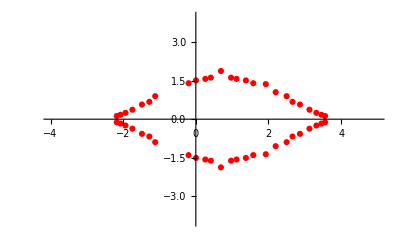

```mathematica
E1=ListPlot[ReIm[Result2],PlotStyle->Red,  PlotRange->{{-4,5},{-4,4}} ]
```

```mathematica
L=FareySequence[40];
Roots55={};
For[n=1,n≤Length[L],n++,If[Max[ContinuedFraction[L[[n]]]]<15,
{p=Numerator[L[[n]]];q=Denominator[L[[n]]];
X=NRoots[FareyPolynomial[p,q,α,β]==-2,z,10];
For[m=1,m≤Length[X],m++,Roots55=Append[Roots55,{Re[X[[m]][[2]]], Im[X[[m]][[2]]]}]]}]]
```

Part::partd: Part specification z⟦2⟧ is longer than depth of object.

Part::partd: Part specification 4.⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 5+5 ⅇ^(-(2 ⅈ π)/5)+5 ⅇ^((2 ⅈ π)/5)+5 ⅇ^(-(4 ⅈ π)/5)+5 ⅇ^((4 ⅈ π)/5).

```mathematica
Length[Roots55]
```

11030

```mathematica
Roots55
```

{{Re[z⟦2⟧],Im[z⟦2⟧]},{Re[4.⟦2⟧],Im[4.⟦2⟧]},{-0.0012807133,0.02566569164},11024,{1.385143801,0.022266763},{Re[z⟦2⟧],Im[z⟦2⟧]},{Re[(-2.618033989+0. ⅈ)⟦2⟧],Im[(-2.618033989+0. ⅈ)⟦2⟧]}}
 |  |  |  |

Part::partd: Part specification 4.⟦2⟧ is longer than depth of object.

Part::partd: Part specification (-2.61803+0. ⅈ)⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

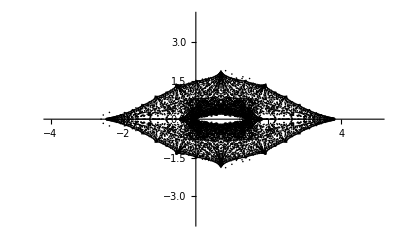

```mathematica
ListPlot[Roots55,PlotStyle->Black, PlotRange->{{-4,5},{-4,4}} ]
```

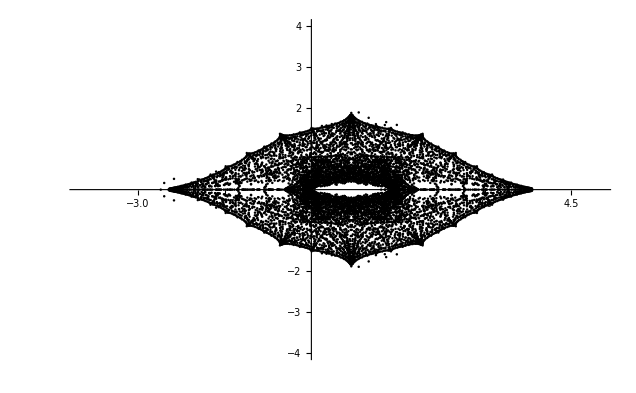
```mathematica
Pic55=-Graphics-
```

```mathematica
Result4={};
For[i=1, i<Length[B]+1, i++,
{G2=Solve[B[[i]]==s,z];
{Result4=AppendTo[Result4,G2],Print[G2]}}]
```

```mathematica
A6=Flatten[N[z]/.Result4];
```

```mathematica
Length[A6]
```

173

```mathematica
Length[Result4]
```

26

```mathematica
l1=ParametricPlot[{Re[A6[[1]]],Im[A6[[1]]]},{s,-20,-2}]
```

```mathematica
l10=ParametricPlot[{Re[A6[[10]]],Im[A6[[10]]]},{s,-10,-2},MaxRecursion->1]
```

```mathematica
l3=ParametricPlot[{Re[A6[[3]]],Im[A6[[3]]]},{s,-10,-2},MaxRecursion->2]
```

```mathematica
ll3=ParametricPlot[{2Re[A6[[1]]]-Re[A6[[3]]],Im[A6[[3]]]},{s,-10,-2},MaxRecursion->2]
```

```mathematica
l4=ParametricPlot[{Re[A6[[4]]],Im[A6[[4]]]},{s,-10,-2}]
```

```mathematica
ll4=ParametricPlot[{2Re[A6[[1]]]-Re[A6[[4]]],Im[A6[[4]]]},{s,-10,-2},MaxRecursion->2]
```

```mathematica
l2=ParametricPlot[{Re[A6[[2]]],Im[A6[[2]]]},{s,-10,-2}]
```

```mathematica
ll2=ParametricPlot[{2Re[A6[[1]]]-Re[A6[[2]]],Im[A6[[2]]]},{s,-10,-2},MaxRecursion->2]
```

```mathematica
l26=ParametricPlot[{Re[A6[[26]]],Im[A6[[26]]]},{s,-20,-2},MaxRecursion->2]
```

```mathematica
l25=ParametricPlot[{Re[A6[[25]]],Im[A6[[25]]]},{s,-20,-2},MaxRecursion->1]
```

```mathematica
l30=ParametricPlot[{Re[A6[[30]]],Im[A6[[30]]]},{s,-20,-2},MaxRecursion->2]
```

```mathematica
l29=ParametricPlot[{Re[A6[[29]]],Im[A6[[29]]]},{s,-20,-2},MaxRecursion->2]
```

```mathematica
l40=ParametricPlot[{Re[A6[[40]]],Im[A6[[40]]]},{s,-20,-2},MaxRecursion->2]
```

```mathematica
l41=ParametricPlot[{Re[A6[[41]]],Im[A6[[41]]]},{s,-20,-2},MaxRecursion->1]
```

```mathematica
l76=ParametricPlot[{Re[A6[[76]]],Im[A6[[76]]]},{s,-20,-2},MaxRecursion->2]
```

```mathematica
l75=ParametricPlot[{Re[A6[[75]]],Im[A6[[75]]]},{s,-20,-2},MaxRecursion->1]
```

```mathematica
l82=ParametricPlot[{Re[A6[[82]]],Im[A6[[82]]]},{s,-20,-2},MaxRecursion->2]
```

```mathematica
l81=ParametricPlot[{Re[A6[[81]]],Im[A6[[81]]]},{s,-20,-2},MaxRecursion->1]
```

```mathematica
l106=ParametricPlot[{Re[A6[[106]]],Im[A6[[106]]]},{s,-20,-2},MaxRecursion->1]
```

```mathematica
l107=ParametricPlot[{Re[A6[[107]]],Im[A6[[107]]]},{s,-20,-2},MaxRecursion->1]
```

```mathematica
Result3={};
For[i=1, i<Length[B]+1, i++,
{G1=Solve[B[[i]]==-2+t ⅈ,z];
{Result3=AppendTo[Result3,G1],Print[G1]}}]
```

```mathematica
Length[Result3]
```

26

```mathematica
A5=Flatten[N[z]/.Result3]
```

```mathematica
Length[A5]
```

173

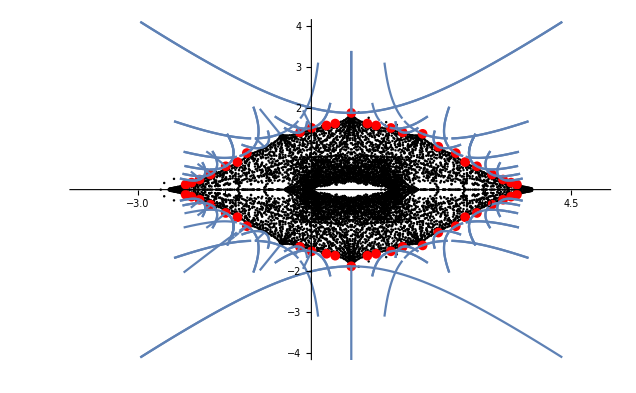

```mathematica
Show[Pic55,E1,l1,l2,ll2,ll3,ll4,l25,l26,l29,l30,l40,l41,l75,l76,l81,l82,l106,l107,l10,c1,cc1,ccc1,cccc1,c2,cc2,ccc2,c3,cc3,ccc3,cccc3,b3,bb3,bbb3,bbbb3,cc4,cccc4,bb4,bbbb4,c10,cc10,ccc10,cccc10,b10,bb10,bbb10,bbbb10,c11,cc11,ccc11,cccc11,b11,bb11,bbb11,bbbb11,c17,cc17,b17,cccc17,bbb17,bb17,c26,cc26,ccc26,cccc26,b26,bbb26,bbbb26,c106,cc106,ccc106,cccc106,b106,bb106,bbb106,bbbb106,c106,cc107,ccc107,cccc107,b107,bb107,bbb107,bbbb107,c30,cc30,ccc30,cccc30,b30,bb30,bbb30,bbbb30,c40,cc40,c76,cc76,ccc76,cccc76,b76,bb76,bbb76,bbbb76,ccc40,cccc40,b40,bb40,c82,cc82,ccc82,cccc82,b82,bb82,bbb82,bbbb82,bbb40,bbbb40,c25,cc25,ccc25,cccc25,b25,bb25,bbb25,bbbb25,c29,ccc29,cccc29,b29,bb29,bbb29,bbbb29,c41,cc41,ccc41,cccc41,b41,bb41,bbb41,bbbb41,c75,cc75,ccc75,cccc75,b75,bb75,bbb75,bbbb75,c81,cc81,ccc81,cccc81,b81,bb81,bbb81,bbbb81,PlotRange->{{-4,5},{-4,4}}]
```

```mathematica
Pic99=
```

```mathematica
c1=ParametricPlot[{Re[A5[[1]]],Im[A5[[1]]]},{t,-30,-0.0001},MaxRecursion->1]
```

```mathematica
cc1=ParametricPlot[{Re[A5[[1]]],Im[A5[[1]]]},{t,0.0001,30},MaxRecursion->1]
```

```mathematica
c2=ParametricPlot[{Re[A5[[2]]],Im[A5[[2]]]},{t,-30,-0.0001},MaxRecursion->1]
```

```mathematica
cc2=ParametricPlot[{Re[A5[[2]]],Im[A5[[2]]]},{t,0.0001,30},MaxRecursion->1]
```

```mathematica
ccc2=ParametricPlot[{Re[A5[[2]]],-Im[A5[[2]]]},{t,-30,-0.0001},MaxRecursion->1]
```

```mathematica
c3=ParametricPlot[{Re[A5[[3]]],Im[A5[[3]]]},{t,-30,-0.0001},MaxRecursion->1]
cc3=ParametricPlot[{Re[A5[[3]]],Im[A5[[3]]]},{t,0.0001,30},MaxRecursion->1]
ccc3=ParametricPlot[{Re[A5[[3]]],-Im[A5[[3]]]},{t,-30,-0.0001},MaxRecursion->1]
cccc3=ParametricPlot[{Re[A5[[3]]],-Im[A5[[3]]]},{t,0.0001,30},MaxRecursion->1]

bb3=ParametricPlot[{2(0.6909830056250525)-Re[A5[[3]]],Im[A5[[3]]]},{t,0.0001,30},MaxRecursion->1]
bbb3=ParametricPlot[{2(0.6909830056250525)-Re[A5[[3]]],-Im[A5[[3]]]},{t,-30,-0.0001},MaxRecursion->1]
bbbb3=ParametricPlot[{2(0.6909830056250525)-Re[A5[[3]]],-Im[A5[[3]]]},{t,0.0001,30},MaxRecursion->1]
```

```mathematica
b3=ParametricPlot[{2(0.6909830056250525)-Re[A5[[3]]],Im[A5[[3]]]},{t,-30,-0.0001},MaxRecursion->1]
```

```mathematica
c4=ParametricPlot[{Re[A5[[4]]],Im[A5[[4]]]},{t,-30,-0.0001},MaxRecursion->1]
cc4=ParametricPlot[{Re[A5[[4]]],Im[A5[[4]]]},{t,0.0001,30},MaxRecursion->1]
ccc4=ParametricPlot[{Re[A5[[4]]],-Im[A5[[4]]]},{t,-30,-0.0001},MaxRecursion->1]
cccc4=ParametricPlot[{Re[A5[[4]]],-Im[A5[[4]]]},{t,0.0001,30},MaxRecursion->1]
b4=ParametricPlot[{2(0.6909830056250525)-Re[A5[[4]]],Im[A5[[4]]]},{t,-30,-0.0001},MaxRecursion->1]
bb4=ParametricPlot[{2(0.6909830056250525)-Re[A5[[4]]],Im[A5[[4]]]},{t,0.0001,30},MaxRecursion->1]
bbb4=ParametricPlot[{2(0.6909830056250525)-Re[A5[[4]]],-Im[A5[[4]]]},{t,-30,-0.0001},MaxRecursion->1]
bbbb4=ParametricPlot[{2(0.6909830056250525)-Re[A5[[4]]],-Im[A5[[4]]]},{t,0.0001,30},MaxRecursion->1]
```

```mathematica
c10=ParametricPlot[{Re[A5[[10]]],Im[A5[[10]]]},{t,-30,-0.0001},MaxRecursion->1]
cc10=ParametricPlot[{Re[A5[[10]]],Im[A5[[10]]]},{t,0.0001,30},MaxRecursion->1]
ccc10=ParametricPlot[{Re[A5[[10]]],-Im[A5[[10]]]},{t,-30,-0.0001},MaxRecursion->1]
cccc10=ParametricPlot[{Re[A5[[10]]],-Im[A5[[10]]]},{t,0.0001,30},MaxRecursion->1]
b10=ParametricPlot[{2(0.6909830056250525)-Re[A5[[10]]],Im[A5[[10]]]},{t,-30,-0.0001},MaxRecursion->1]
bb10=ParametricPlot[{2(0.6909830056250525)-Re[A5[[10]]],Im[A5[[10]]]},{t,0.0001,30},MaxRecursion->1]
bbb10=ParametricPlot[{2(0.6909830056250525)-Re[A5[[10]]],-Im[A5[[10]]]},{t,-30,-0.0001},MaxRecursion->1]
bbbb10=ParametricPlot[{2(0.6909830056250525)-Re[A5[[10]]],-Im[A5[[10]]]},{t,0.0001,30},MaxRecursion->1]
```

```mathematica
c11=ParametricPlot[{Re[A5[[11]]],Im[A5[[11]]]},{t,-30,-0.0001},MaxRecursion->1]
cc11=ParametricPlot[{Re[A5[[11]]],Im[A5[[11]]]},{t,0.0001,30},MaxRecursion->1]
ccc11=ParametricPlot[{Re[A5[[11]]],-Im[A5[[11]]]},{t,-30,-0.0001},MaxRecursion->1]
cccc11=ParametricPlot[{Re[A5[[11]]],-Im[A5[[11]]]},{t,0.0001,30},MaxRecursion->1]
b11=ParametricPlot[{2(0.6909830056250525)-Re[A5[[11]]],Im[A5[[11]]]},{t,-30,-0.0001},MaxRecursion->1]
bb11=ParametricPlot[{2(0.6909830056250525)-Re[A5[[11]]],Im[A5[[11]]]},{t,0.0001,30},MaxRecursion->1]
bbb11=ParametricPlot[{2(0.6909830056250525)-Re[A5[[11]]],-Im[A5[[11]]]},{t,-30,-0.0001},MaxRecursion->1]
bbbb11=ParametricPlot[{2(0.6909830056250525)-Re[A5[[11]]],-Im[A5[[11]]]},{t,0.0001,30},MaxRecursion->1]
```

```mathematica
c17=ParametricPlot[{Re[A5[[17]]],Im[A5[[17]]]},{t,-30,-0.0001},MaxRecursion->1]
cc17=ParametricPlot[{Re[A5[[17]]],Im[A5[[17]]]},{t,0.0001,30},MaxRecursion->1]
ccc17=ParametricPlot[{Re[A5[[17]]],-Im[A5[[39]]]},{t,-30,-0.0001},MaxRecursion->1]
cccc17=ParametricPlot[{Re[A5[[17]]],-Im[A5[[17]]]},{t,0.0001,30},MaxRecursion->1]
b17=ParametricPlot[{2(0.6909830056250525)-Re[A5[[17]]],Im[A5[[17]]]},{t,-30,-0.0001},MaxRecursion->1]
bb17=ParametricPlot[{2(0.6909830056250525)-Re[A5[[17]]],Im[A5[[17]]]},{t,0.0001,30},MaxRecursion->1]
bbb17=ParametricPlot[{2(0.6909830056250525)-Re[A5[[17]]],-Im[A5[[17]]]},{t,-30,-0.0001},MaxRecursion->1]
bbbb17=ParametricPlot[{2(0.6909830056250525)-Re[A5[[39]]],-Im[A5[[17]]]},{t,0.0001,30},MaxRecursion->1]
```

```mathematica
c26=ParametricPlot[{Re[A5[[26]]],Im[A5[[26]]]},{t,-30,-0.0001},MaxRecursion->1]
cc26=ParametricPlot[{Re[A5[[26]]],Im[A5[[26]]]},{t,0.0001,30},MaxRecursion->1]
ccc26=ParametricPlot[{Re[A5[[26]]],-Im[A5[[26]]]},{t,-30,-0.0001},MaxRecursion->1]
cccc26=ParametricPlot[{Re[A5[[26]]],-Im[A5[[26]]]},{t,0.0001,30},MaxRecursion->1]
b26=ParametricPlot[{2(0.6909830056250525)-Re[A5[[26]]],Im[A5[[26]]]},{t,-30,-0.0001},MaxRecursion->1]
bb26=ParametricPlot[{2(0.6909830056250525)-Re[A5[[26]]],Im[A5[[26]]]},{t,0.0001,30},MaxRecursion->1]
bbb26=ParametricPlot[{2(0.6909830056250525)-Re[A5[[26]]],-Im[A5[[26]]]},{t,-30,-0.0001},MaxRecursion->1]
bbbb26=ParametricPlot[{2(0.6909830056250525)-Re[A5[[26]]],-Im[A5[[26]]]},{t,0.0001,30},MaxRecursion->1]
```

```mathematica
c25=ParametricPlot[{Re[A5[[25]]],Im[A5[[25]]]},{t,-30,-0.0001},MaxRecursion->1]
cc25=ParametricPlot[{Re[A5[[25]]],Im[A5[[25]]]},{t,0.0001,30},MaxRecursion->1]
ccc25=ParametricPlot[{Re[A5[[25]]],-Im[A5[[25]]]},{t,-30,-0.0001},MaxRecursion->1]
cccc25=ParametricPlot[{Re[A5[[25]]],-Im[A5[[25]]]},{t,0.0001,30},MaxRecursion->1]
b25=ParametricPlot[{2(0.6909830056250525)-Re[A5[[25]]],Im[A5[[25]]]},{t,-30,-0.0001},MaxRecursion->1]
bbb25=ParametricPlot[{2(0.6909830056250525)-Re[A5[[25]]],-Im[A5[[25]]]},{t,-30,-0.0001},MaxRecursion->1]
bbbb25=ParametricPlot[{2(0.6909830056250525)-Re[A5[[25]]],-Im[A5[[25]]]},{t,0.0001,30},MaxRecursion->1]
```

```mathematica
Show[Pic55,E1,c26,cc26,ccc26,cccc26,b26,bb26,bbb26,bbbb26,c25,cc25,ccc25,cccc25,b25,bb25,bbb25,bbbb25,PlotRange->{{-4,5},{-4,4}}]
```

```mathematica
bb25=ParametricPlot[{2(0.6909830056250525)-Re[A5[[25]]],Im[A5[[25]]]},{t,0.0001,30},MaxRecursion->1]
```

```mathematica
c29=ParametricPlot[{Re[A5[[29]]],Im[A5[[29]]]},{t,-30,-0.0001},MaxRecursion->1]
cc29=ParametricPlot[{Re[A5[[25]]],Im[A5[[29]]]},{t,0.0001,30},MaxRecursion->1]
ccc29=ParametricPlot[{Re[A5[[29]]],-Im[A5[[29]]]},{t,-30,-0.0001},MaxRecursion->1]
cccc29=ParametricPlot[{Re[A5[[29]]],-Im[A5[[29]]]},{t,0.0001,30},MaxRecursion->1]
b29=ParametricPlot[{2(0.6909830056250525)-Re[A5[[29]]],Im[A5[[29]]]},{t,-30,-0.0001},MaxRecursion->1]
bbb29=ParametricPlot[{2(0.6909830056250525)-Re[A5[[29]]],-Im[A5[[29]]]},{t,-30,-0.0001},MaxRecursion->1]
bbbb29=ParametricPlot[{2(0.6909830056250525)-Re[A5[[29]]],-Im[A5[[29]]]},{t,0.0001,30},MaxRecursion->1]
bb29=ParametricPlot[{2(0.6909830056250525)-Re[A5[[29]]],Im[A5[[29]]]},{t,0.0001,30},MaxRecursion->1]
Show[Pic55,E1,c29,ccc29,cccc29,b29,bb29,bbb29,bbbb29,PlotRange->{{-4,5},{-4,4}}]
```

```mathematica
c30=ParametricPlot[{Re[A5[[30]]],Im[A5[[30]]]},{t,-30,-0.0001},MaxRecursion->1]
cc30=ParametricPlot[{Re[A5[[30]]],Im[A5[[30]]]},{t,0.0001,30},MaxRecursion->1]
ccc30=ParametricPlot[{Re[A5[[30]]],-Im[A5[[30]]]},{t,-30,-0.0001},MaxRecursion->1]
cccc30=ParametricPlot[{Re[A5[[30]]],-Im[A5[[30]]]},{t,0.0001,30},MaxRecursion->1]
b30=ParametricPlot[{2(0.6909830056250525)-Re[A5[[30]]],Im[A5[[30]]]},{t,-30,-0.0001},MaxRecursion->1]
bb30=ParametricPlot[{2(0.6909830056250525)-Re[A5[[30]]],Im[A5[[30]]]},{t,0.0001,30},MaxRecursion->1]
bbb30=ParametricPlot[{2(0.6909830056250525)-Re[A5[[30]]],-Im[A5[[30]]]},{t,-30,-0.0001},MaxRecursion->1]
bbbb30=ParametricPlot[{2(0.6909830056250525)-Re[A5[[30]]],-Im[A5[[30]]]},{t,0.0001,30},MaxRecursion->1]
```

```mathematica
Show[Pic55,E1,c30,cc30,ccc30,cccc30,b30,bb30,bbb30,bbbb30,PlotRange->{{-4,5},{-4,4}}]
```

```mathematica
c40=ParametricPlot[{Re[A5[[40]]],Im[A5[[40]]]},{t,-30,-0.0001},MaxRecursion->1]
cc40=ParametricPlot[{Re[A5[[40]]],Im[A5[[40]]]},{t,0.0001,30},MaxRecursion->1]
ccc40=ParametricPlot[{Re[A5[[40]]],-Im[A5[[40]]]},{t,-30,-0.0001},MaxRecursion->1]
cccc40=ParametricPlot[{Re[A5[[40]]],-Im[A5[[40]]]},{t,0.0001,30},MaxRecursion->1]
b40=ParametricPlot[{2(0.6909830056250525)-Re[A5[[40]]],Im[A5[[40]]]},{t,-30,-0.0001},MaxRecursion->1]
bb40=ParametricPlot[{2(0.6909830056250525)-Re[A5[[40]]],Im[A5[[40]]]},{t,0.0001,30},MaxRecursion->1]
bbb40=ParametricPlot[{2(0.6909830056250525)-Re[A5[[40]]],-Im[A5[[40]]]},{t,-30,-0.0001},MaxRecursion->1]
bbbb40=ParametricPlot[{2(0.6909830056250525)-Re[A5[[40]]],-Im[A5[[40]]]},{t,0.0001,30},MaxRecursion->1]
```

```mathematica
Show[Pic55,E1,c40,cc40,ccc40,cccc40,b40,bb40,bbb40,bbbb40,PlotRange->{{-4,5},{-4,4}}]
```

```mathematica
c41=ParametricPlot[{Re[A5[[41]]],Im[A5[[41]]]},{t,-30,-0.0001},MaxRecursion->1]
cc41=ParametricPlot[{Re[A5[[41]]],Im[A5[[41]]]},{t,0.0001,30},MaxRecursion->1]
ccc41=ParametricPlot[{Re[A5[[41]]],-Im[A5[[41]]]},{t,-30,-0.0001},MaxRecursion->1]
cccc41=ParametricPlot[{Re[A5[[41]]],-Im[A5[[41]]]},{t,0.0001,30},MaxRecursion->1]
b41=ParametricPlot[{2(0.6909830056250525)-Re[A5[[41]]],Im[A5[[41]]]},{t,-30,-0.0001},MaxRecursion->1]
bb41=ParametricPlot[{2(0.6909830056250525)-Re[A5[[41]]],Im[A5[[41]]]},{t,0.0001,30},MaxRecursion->1]
bbb41=ParametricPlot[{2(0.6909830056250525)-Re[A5[[41]]],-Im[A5[[41]]]},{t,-30,-0.0001},MaxRecursion->1]
bbbb41=ParametricPlot[{2(0.6909830056250525)-Re[A5[[41]]],-Im[A5[[41]]]},{t,0.0001,30},MaxRecursion->1]
Show[Pic55,E1,c41,cc41,ccc41,cccc41,b41,bb41,bbb41,bbbb41,PlotRange->{{-4,5},{-4,4}}]
```

```mathematica
c76=ParametricPlot[{Re[A5[[76]]],Im[A5[[76]]]},{t,-30,-0.0001},MaxRecursion->1]
cc76=ParametricPlot[{Re[A5[[76]]],Im[A5[[76]]]},{t,0.0001,30},MaxRecursion->1]
ccc76=ParametricPlot[{Re[A5[[76]]],-Im[A5[[76]]]},{t,-30,-0.0001},MaxRecursion->1]
cccc76=ParametricPlot[{Re[A5[[76]]],-Im[A5[[76]]]},{t,0.0001,30},MaxRecursion->1]
b76=ParametricPlot[{2(0.6909830056250525)-Re[A5[[76]]],Im[A5[[76]]]},{t,-30,-0.0001},MaxRecursion->1]
bb76=ParametricPlot[{2(0.6909830056250525)-Re[A5[[76]]],Im[A5[[76]]]},{t,0.0001,30},MaxRecursion->1]
bbb76=ParametricPlot[{2(0.6909830056250525)-Re[A5[[76]]],-Im[A5[[76]]]},{t,-30,-0.0001},MaxRecursion->1]
bbbb76=ParametricPlot[{2(0.6909830056250525)-Re[A5[[76]]],-Im[A5[[76]]]},{t,0.0001,30},MaxRecursion->1]
```

```mathematica
Show[Pic55,E1,c76,cc76,ccc76,cccc76,b76,bb76,bbb76,bbbb76,PlotRange->{{-4,5},{-4,4}}]
```

```mathematica
c75=ParametricPlot[{Re[A5[[75]]],Im[A5[[75]]]},{t,-30,-0.0001},MaxRecursion->1]
cc75=ParametricPlot[{Re[A5[[75]]],Im[A5[[75]]]},{t,0.0001,30},MaxRecursion->1]
ccc75=ParametricPlot[{Re[A5[[75]]],-Im[A5[[75]]]},{t,-30,-0.0001},MaxRecursion->1]
cccc75=ParametricPlot[{Re[A5[[75]]],-Im[A5[[75]]]},{t,0.0001,30},MaxRecursion->1]
b75=ParametricPlot[{2(0.6909830056250525)-Re[A5[[75]]],Im[A5[[75]]]},{t,-30,-0.0001},MaxRecursion->1]
bb75=ParametricPlot[{2(0.6909830056250525)-Re[A5[[75]]],Im[A5[[75]]]},{t,0.0001,30},MaxRecursion->1]
bbb75=ParametricPlot[{2(0.6909830056250525)-Re[A5[[75]]],-Im[A5[[75]]]},{t,-30,-0.0001},MaxRecursion->1]
bbbb75=ParametricPlot[{2(0.6909830056250525)-Re[A5[[75]]],-Im[A5[[75]]]},{t,0.0001,30},MaxRecursion->1]
Show[Pic55,E1,c76,cc76,ccc76,cccc76,b76,bb76,bbb76,bbbb76,PlotRange->{{-4,5},{-4,4}}]
```

```mathematica
Show[Pic55,E1,c75,cc75,ccc75,cccc75,b75,bb75,bbb75,bbbb75,PlotRange->{{-4,5},{-4,4}}]
```

```mathematica
c82=ParametricPlot[{Re[A5[[82]]],Im[A5[[82]]]},{t,-30,-0.0001},MaxRecursion->1]
cc82=ParametricPlot[{Re[A5[[82]]],Im[A5[[82]]]},{t,0.0001,30},MaxRecursion->1]
ccc82=ParametricPlot[{Re[A5[[82]]],-Im[A5[[82]]]},{t,-30,-0.0001},MaxRecursion->1]
cccc82=ParametricPlot[{Re[A5[[82]]],-Im[A5[[82]]]},{t,0.0001,30},MaxRecursion->1]
b82=ParametricPlot[{2(0.6909830056250525)-Re[A5[[82]]],Im[A5[[82]]]},{t,-30,-0.0001},MaxRecursion->1]
bb82=ParametricPlot[{2(0.6909830056250525)-Re[A5[[82]]],Im[A5[[82]]]},{t,0.0001,30},MaxRecursion->1]
bbb82=ParametricPlot[{2(0.6909830056250525)-Re[A5[[82]]],-Im[A5[[82]]]},{t,-30,-0.0001},MaxRecursion->1]
bbbb82=ParametricPlot[{2(0.6909830056250525)-Re[A5[[82]]],-Im[A5[[82]]]},{t,0.0001,30},MaxRecursion->1]
```

```mathematica
Show[Pic55,E1,c82,cc82,ccc82,cccc82,b82,bb82,bbb82,bbbb82,PlotRange->{{-4,5},{-4,4}}]
```

```mathematica
c81=ParametricPlot[{Re[A5[[81]]],Im[A5[[81]]]},{t,-30,-0.0001},MaxRecursion->1]
cc81=ParametricPlot[{Re[A5[[81]]],Im[A5[[81]]]},{t,0.0001,30},MaxRecursion->1]
ccc81=ParametricPlot[{Re[A5[[81]]],-Im[A5[[81]]]},{t,-30,-0.0001},MaxRecursion->1]
cccc81=ParametricPlot[{Re[A5[[81]]],-Im[A5[[81]]]},{t,0.0001,30},MaxRecursion->1]
b81=ParametricPlot[{2(0.6909830056250525)-Re[A5[[81]]],Im[A5[[81]]]},{t,-30,-0.0001},MaxRecursion->1]
bb81=ParametricPlot[{2(0.6909830056250525)-Re[A5[[81]]],Im[A5[[81]]]},{t,0.0001,30},MaxRecursion->1]
bbb81=ParametricPlot[{2(0.6909830056250525)-Re[A5[[81]]],-Im[A5[[81]]]},{t,-30,-0.0001},MaxRecursion->1]
bbbb81=ParametricPlot[{2(0.6909830056250525)-Re[A5[[81]]],-Im[A5[[81]]]},{t,0.0001,30},MaxRecursion->1]
Show[Pic55,E1,c81,cc81,ccc81,cccc81,b81,bb81,bbb81,bbbb81,PlotRange->{{-4,5},{-4,4}}]
```

```mathematica
c106=ParametricPlot[{Re[A5[[106]]],Im[A5[[106]]]},{t,-30,-0.0001},MaxRecursion->1]
cc106=ParametricPlot[{Re[A5[[106]]],Im[A5[[106]]]},{t,0.0001,30},MaxRecursion->1]
ccc106=ParametricPlot[{Re[A5[[106]]],-Im[A5[[106]]]},{t,-30,-0.0001},MaxRecursion->1]
cccc106=ParametricPlot[{Re[A5[[106]]],-Im[A5[[106]]]},{t,0.0001,30},MaxRecursion->1]
b106=ParametricPlot[{2(0.6909830056250525)-Re[A5[[106]]],Im[A5[[106]]]},{t,-30,-0.0001},MaxRecursion->1]
bb106=ParametricPlot[{2(0.6909830056250525)-Re[A5[[106]]],Im[A5[[106]]]},{t,0.0001,30},MaxRecursion->1]
bbb106=ParametricPlot[{2(0.6909830056250525)-Re[A5[[106]]],-Im[A5[[106]]]},{t,-30,-0.0001},MaxRecursion->1]
bbbb106=ParametricPlot[{2(0.6909830056250525)-Re[A5[[106]]],-Im[A5[[106]]]},{t,0.0001,30},MaxRecursion->1]
```

```mathematica
Show[Pic55,E1,c106,cc106,ccc106,cccc106,b106,bb106,bbb106,bbbb106,c106,cc107,ccc107,cccc107,b107,bb107,bbb107,bbbb107,PlotRange->{{-4,5},{-4,4}}]
```

```mathematica
c107=ParametricPlot[{Re[A5[[107]]],Im[A5[[107]]]},{t,-30,-0.0001},MaxRecursion->1]
cc107=ParametricPlot[{Re[A5[[107]]],Im[A5[[107]]]},{t,0.0001,30},MaxRecursion->1]
ccc107=ParametricPlot[{Re[A5[[107]]],-Im[A5[[107]]]},{t,-30,-0.0001},MaxRecursion->1]
cccc107=ParametricPlot[{Re[A5[[107]]],-Im[A5[[107]]]},{t,0.0001,30},MaxRecursion->1]
b107=ParametricPlot[{2(0.6909830056250525)-Re[A5[[107]]],Im[A5[[107]]]},{t,-30,-0.0001},MaxRecursion->1]
bb107=ParametricPlot[{2(0.6909830056250525)-Re[A5[[107]]],Im[A5[[107]]]},{t,0.0001,30},MaxRecursion->1]
bbb107=ParametricPlot[{2(0.6909830056250525)-Re[A5[[107]]],-Im[A5[[107]]]},{t,-30,-0.0001},MaxRecursion->1]
bbbb107=ParametricPlot[{2(0.6909830056250525)-Re[A5[[107]]],-Im[A5[[107]]]},{t,0.0001,30},MaxRecursion->1]
```

```mathematica
Green points are (5,5) cases.
1.64369+1.82775ⅈ, -2.61803, -.310577+1.60586ⅈ,-3.61803, -1.76538+1.5693ⅈ,-1.19098+0.981593ⅈ,-2.61803,-2,-3,-1,-2+.786151ⅈ, -.190983+0.981593ⅈ, -1.19098+1.8925ⅈ
Yellow points  are (5,2) cases.
```

```mathematica
H={1.64369+1.82775ⅈ, -2.61803, -.310577+1.60586ⅈ,-3.61803, -1.76538+1.5693ⅈ,-1.19098+0.981593ⅈ,-2.61803,-2,-3,-1,-2+.786151ⅈ, -.190983+0.981593ⅈ, -1.19098+1.8925ⅈ};
```

```mathematica
HH=Table[Solve[Gamma (Gamma-4 Sin[π/5] Sin[π/5])==H[[i]],Gamma],{i,1,Length[H]}]
```

```mathematica
HHH=Flatten[Gamma/.HH]
```

```mathematica
W=ListPlot[ReIm[HHH],PlotStyle ->Green,PlotRange->{{-4,5},{-4,4}} ]
```

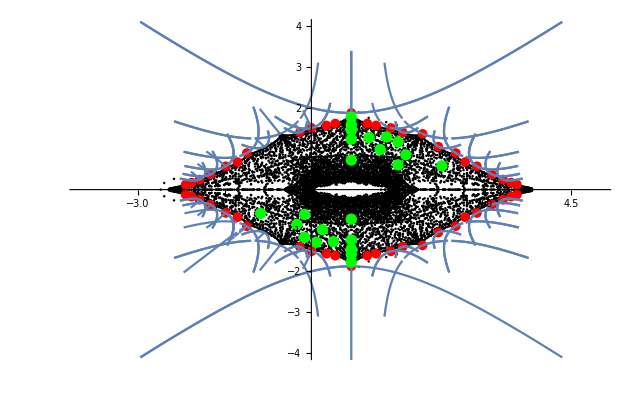
```mathematica
Pic88=-Graphics-
```

```mathematica
ListPlot[Roots55,PlotStyle->Black, PlotRange->{{-4,5},{-4,4}} ]
```

Part::partd: Part specification 4.⟦2⟧ is longer than depth of object.

Part::partd: Part specification (-2.61803+0. ⅈ)⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

```mathematica
L=FareySequence[40];
Roots55={};
For[n=1,n≤Length[L],n++,If[Max[ContinuedFraction[L[[n]]]]<15,
{p=Numerator[L[[n]]];q=Denominator[L[[n]]];
X=NRoots[FareyPolynomial[p,q,α,β]==-2,z,10];
γmax=0;
For[m=1,m≤Length[X],m++,
γ=X[[m]][[2]] (X[[m]][[2]] -4 Sin[π/5] Sin[π/5]);
Roots55=Append[Roots55,{Re[γ], Im[γ]}];
Roots55=Append[Roots55,{Re[γ],- Im[γ]}];
γmax=Max[γmax,Abs[γ]+Abs[γ+(16 Sin[π/5]^2 Sin[π/5]^2)/4]]
];MinEllipse=Append[MinEllipse,γmax]}]];
 Pic44=List[Roots55];
```

```mathematica
Length[FareySequence[100]]
```

3045

```mathematica
ListPlot[Pic44,PlotStyle->{Red,Thick},PlotRange->{{-4,11},{-4,4}}]
```

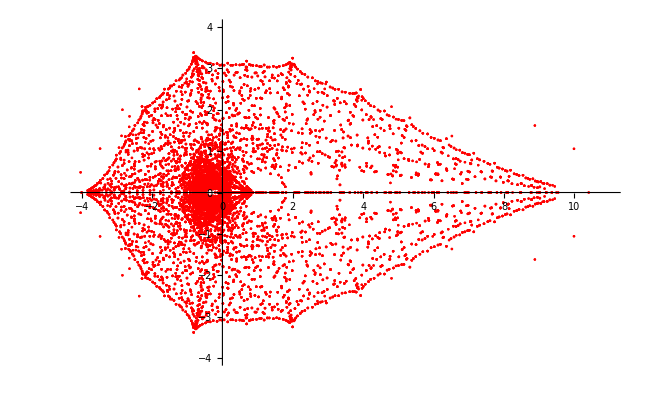
```mathematica
Pic77=-Graphics-
```

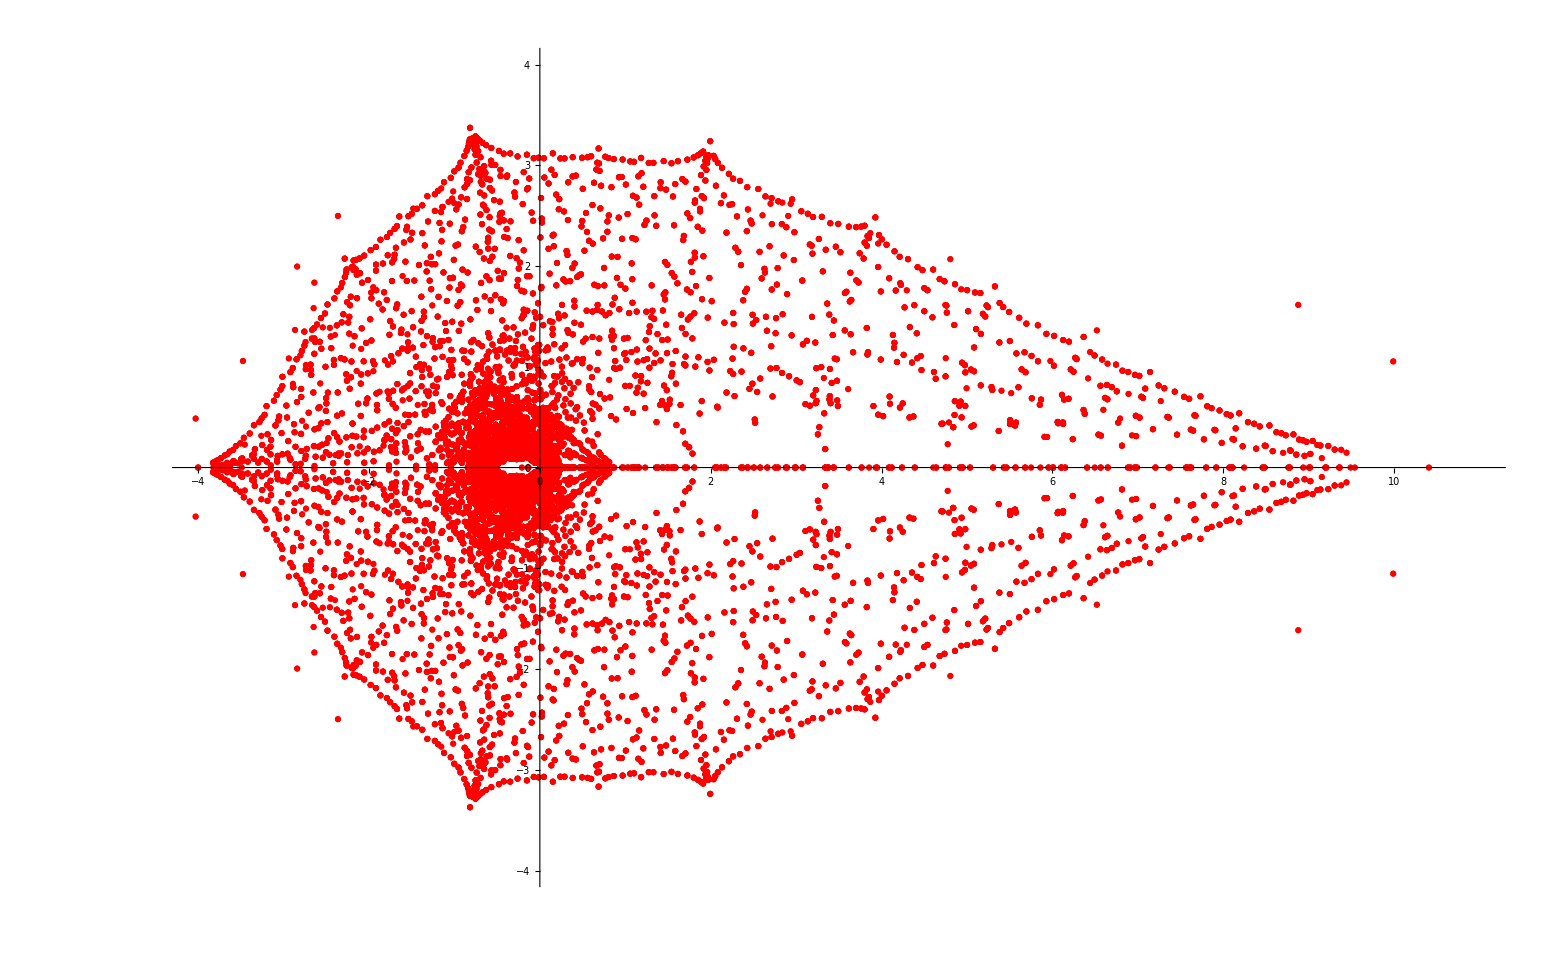

```mathematica
Result2[[1]]
```

0.690983-1.87684 ⅈ

```mathematica
L=FareySequence[40];
AllRoots={};
For[n=1,n≤Length[L],n++,If[Max[ContinuedFraction[L[[n]]]]<15,
{p=Numerator[L[[n]]];q=Denominator[L[[n]]];
γmax=0;
For[m=1,m≤Length[Result2],m++,
γ=Result2[[m]] (Result2[[m]] -4 Sin[π/5] Sin[π/5]);
AllRoots=Append[AllRoots,{Re[γ], Im[γ]}];
AllRoots=Append[AllRoots,{Re[γ],- Im[γ]}];
γmax=Max[γmax,Abs[γ]+Abs[γ+(16 Sin[π/5]^2 Sin[π/5]^2)/4]]
];MinEllipse=Append[MinEllipse,γmax]}]];
 Pic45=List[AllRoots];
```

```mathematica
ListPlot[Pic45,PlotStyle->{Red,Thick},PlotRange->{{-4,11},{-4,4}}]
```